```mathematica
<<QMRITools`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Functions

```mathematica
(*dynamic PCr signal function*)
MakePcr[start_,{{trest_,tex_,trec_,dt_},{pcrEx_,pcrRec_}}]:=Block[{end,func,t},
end=(start Exp[tex/-pcrEx]);
func=Piecewise[{
{start,0<=t<trest},
{start Exp[(t-trest)/-pcrEx],trest<=t<tex+trest},
{end+(start-end)(1-Exp[(t-trest-tex)/-pcrRec]),tex+trest<=t}
}];
Table[func/.t->x,{x,0.,trest+tex+trec,dt}]
]

(*fucntion to simulate spectra*)
SimulateFid[{lw_,rat_,snr_,shift_},{nsamp_,bw_,field_,nuc_},{{trest_,tex_,trec_,dt_},{pcrEx_,pcrRec_}}]:=Block[{names,fids,specs,table,met,metNames,metAmps,dw,gyro,time,specsTS,
pcrAmpB,piinS,pcrt,piint,l,sigma,fid,fidsI},
(*get the basis functions for each *)

pcrAmpB=rat 250;
piinS=78;

pcrt=MakePcr[pcrAmpB(*start value*),{{trest,tex,trec,dt},{pcrEx,pcrRec}}];
piint=pcrAmpB-pcrt+piinS;

l=Length[pcrt];
sigma=pcrAmpB/snr;

dw=1./bw;
gyro=GetGyro[field,nuc];

metNames={"PE","PC","Piex","Piin","GPE","GPC","PCr","ATP","NAD","UDPG"};

{names,fidsI,specs,table}=GetSpectraBasisFunctions[metNames,
BasisSequence->{"PulseAcquire",0}(*sequence and echo time, normally 2 dwell times*)
,SpectraSamples->nsamp,SpectraBandwith->bw,SpectraPpmShift->0,SpectraFieldStrength->field,SpectraNucleus->nuc];
time=GetTimeRange[fidsI[[1]],dw];
fidsI=TimeShiftFid[#,time,lw]&/@fidsI;

(*actual loop for dynamic simulation*)
Table[
metAmps={17,30,39,piint[[i]],0,64,pcrt[[i]],250,18,20};

specs=ShiftSpectra[ShiftedFourier[#],{dw,gyro},RandomReal[{-1,1}shift]]&/@fidsI;
fids=ShiftedInverseFourier[metAmps.specs];

AddNoise[fids,sigma,NoiseType->"Complex"]
,{i,1,l,1}]
]
```

#### Simulation

```mathematica
(*simulation contraints*)
PCrATPratio=4;
lineWidth=30(*Hz*);
snr=40;
shift=0.1;

(*acquisition paramters*)
nsamp=1000;(*number of spectral samples*)
bw=5000;(*acquisition bandwithd*)
field=3;(*field strenght of simulations*)
nuc="31P";(*relevant nucleius*)

(*PCr timings*)
trest=60;(*s*)
tex=160;(*s*)
trec=300;(*s*)
dt=2;(*s*)

(*PCr half times*)
pcrEx=120;
pcrRec=60;
```

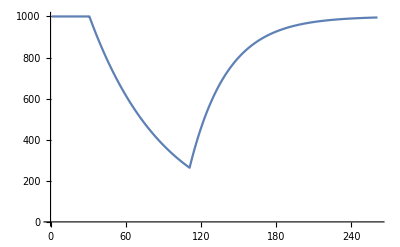

```mathematica
(*plot the PCr function for demonstration*)
pcrPlot=ListLinePlot@(MakePcr[1000(*start value*),{{trest,tex,trec,dt},{pcrEx,pcrRec}}])
```

```mathematica
Export["pcrPlot.jpg",pcrPlot]
```

pcrPlot.jpg

```mathematica
"pcrPlot.jpg"
```

pcrPlot.jpg

```mathematica
(*simulate the FID*)
simFid=SimulateFid[{lineWidth,PCrATPratio,snr,shift},{nsamp,bw,field,nuc},{{trest,tex,trec,dt},{pcrEx,pcrRec}}];
(*convert to spectra*)
simSpec=ShiftedFourier/@simFid;
```

```mathematica
fMax=Max[Abs[simFid]];
sMax=Max[Abs[simSpec]];

dw=1./bw;
gyro=GetGyro[field,nuc];

Manipulate[
Row@{
PlotSpectra[simSpec[[n]],{dw,gyro},PlotRange->{{10,-20},{-1,1}sMax},ImageSize->300,AspectRatio->1],
PlotFid[simFid[[n]],dw,ImageSize->300,AspectRatio->1]
}
,{n,1,Length[simFid],1}]
```

```mathematica
gif=Table[
Row@{
PlotSpectra[simSpec[[n]],{dw,gyro},PlotRange->{{10,-20},{-1,1}sMax},ImageSize->300,AspectRatio->1],
PlotFid[simFid[[n]],dw,ImageSize->300,AspectRatio->1]
}
,{n,1,Length[simFid],4}];
```

```mathematica
Export["dyn.gif",gif,AnimationRepetitions->Infinity,"DisplayDurations"->0.01];
```